## Pràctica 2: NOMBRES COMPLEXOS

### Exercici 1

Donats els nombres complexos següents: z_1=1+ⅈ, z_2=2+3ⅈ, z_3=√2-√5 ⅈ:
(a) Comproveu que z_1^4=-4 (Compte! En Mathematica la unitat imaginària és I). Calculeu z_1-z_2,z_1*z_3 i  z_3^-1.

Observeu que en fer el càlcul de z_3^-1, el Mathematica no retorna el nombre complex en la forma a+bi.

```mathematica
z1= 1 +I
```

1+ⅈ

```mathematica
z2=2 + 3I
```

2+3 ⅈ

```mathematica
z3= Sqrt[2] - Sqrt[5] I
```

√2-ⅈ √5

(b) Executeu les instruccions:

```mathematica
z1=1+I
```

1+ⅈ

```mathematica
s=Sqrt[z1]
```

√(1+ⅈ)

```mathematica
ComplexExpand[s]
```

2^(1/4) Cos[π/8]+ⅈ 2^(1/4) Sin[π/8]

```mathematica
Re[%]
```

2^(1/4) Cos[π/8]

```mathematica
Im[%%]
```

2^(1/4) Sin[π/8]

Quines són les arrels quadrades de z_1? Torneu a calcular z_3^-1, aquesta vegada donant el resultat en la forma a+bi.

```mathematica
Sqrt[z1]
```

√(1+ⅈ)

```mathematica
ComplexExpand[z3 ^{-1}]
```

{(√2)/7+(ⅈ √5)/7}

(c) Esbrineu per a què serveixen les funcions del Mathematica Abs i Arg, i utilitzeu-les per a calcular la forma polar de  z_1,z_2 i  z_3.

```mathematica
Abs[z1]
```

√2

```mathematica
Arg[z1]
```

π/4

```mathematica
Abs[z2]
```

√13

```mathematica
Arg[z2]
```

ArcTan[3/2]

```mathematica
Abs[z3]
```

√7

```mathematica
Arg[z3]
```

-ArcTan[√(5/2)]

### Exercici 2

(a) Esbrineu que fa la funció Conjugate i comproveu la igualtat z*Conjugate[z]=Abs[z]^2 per  z_1,z_2 i  z_3.

```mathematica
z1*Conjugate[z1]==Abs[z1] ^2
```

True

```mathematica
z2*Conjugate[z2]==Abs[z2] ^2
```

True

```mathematica
z3*Conjugate[z3]==Abs[z3] ^2
```

True

(b) Executeu les següents instruccions

```mathematica
z1*Conjugate[z1]==Abs[z1]^2
```

True

```mathematica
z1*Conjugate[z1]==Abs[z1]^2+1
```

False

Que fa "==" ?

```mathematica
Compara les dues instruccions i retorna si es veritat o fals.
```

(c) Doneu valors a n i theta (n ha de ser enter positiu) i verifiqueu la igualtat

```mathematica
Theta = 5
```

5

```mathematica
n=1
```

1

```mathematica
(Cos[theta]+I*Sin[theta])^n==Cos[n*theta]+I*Sin[n*theta]
```

True

(d) Doneu valors enters negatius a n. Es segueix verificant la igualtat anterior?

```mathematica
No.
```

```mathematica
n= -4
```

-4

```mathematica
(Cos[theta]+I*Sin[theta])^n==Cos[n*theta]+I*Sin[n*theta]
```

1/(Cos[theta]+ⅈ Sin[theta])^4==Cos[4 theta]-ⅈ Sin[4 theta]

### Exercici 3

La següent funció ens permetrà visualitzar els nombres complexos:

```mathematica
v[z_]:= Graphics[Arrow[{{0,0},{Re[z],Im[z]}}], Axes ->True]
```

(a) Dibuixem z_1,z_2 i  z_1*z_2

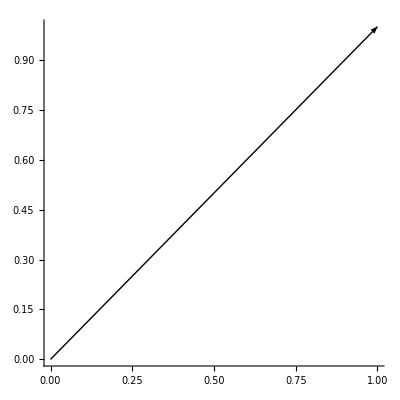

```mathematica
v[z1]
```

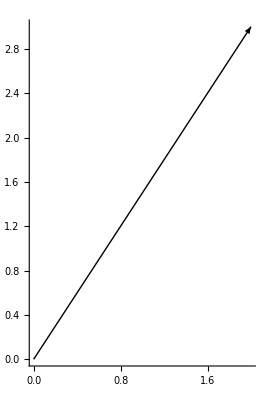

```mathematica
v[z2]
```

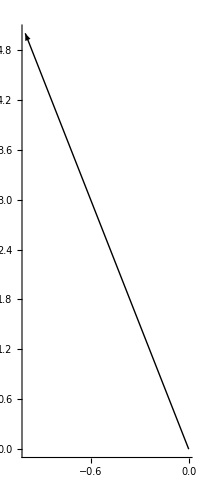

```mathematica
v[z1*z2]
```

Vegem els tres vectors junts

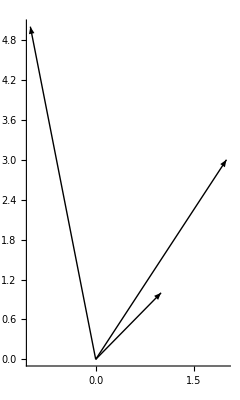

```mathematica
Show[%,%%,%%%]
```

(b) Dibuixem les primeres potències de z_1:

```mathematica
a[i_]:=v[z1^i]
```

```mathematica
a[1]
```

-Graphics-

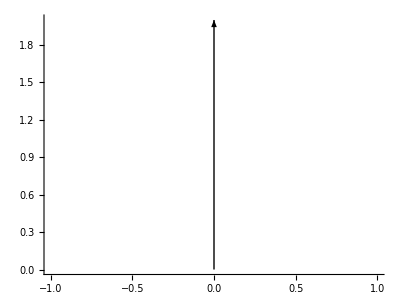

```mathematica
a[2]
```

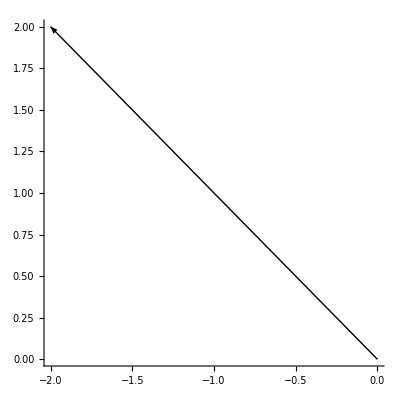

```mathematica
a[3]
```

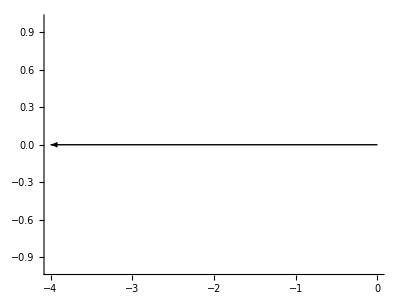

```mathematica
a[4]
```

```mathematica
Show[%,%%,%%%,%%%%]
```

(c) Dibuixeu 1/z_1,Conjugate[z_2], i les cinc primeres potències de  z_3.

```mathematica
v[z_]:= Graphics[Arrow[{{0,0},{Re[z],Im[z]}}], Axes ->True]
```

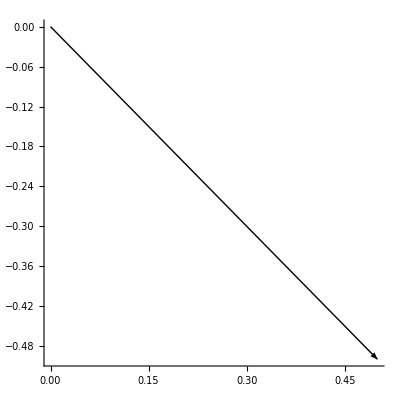

```mathematica
v[1/z1]
```

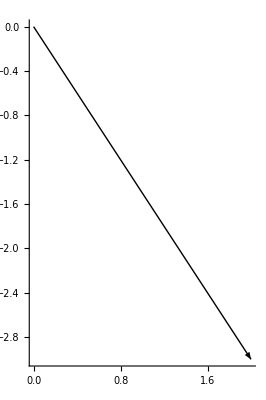

```mathematica
v[Conjugate[z2]]
```

```mathematica
a[i_] :=v[z3 ^i]
```

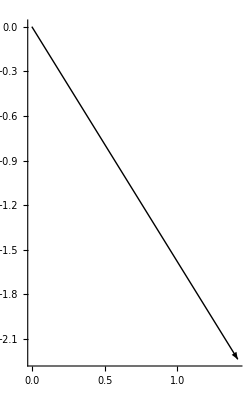

```mathematica
a[1]
```

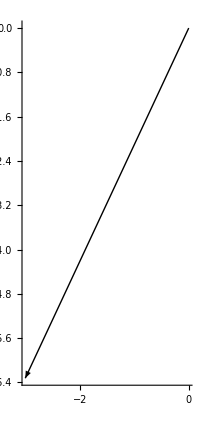

```mathematica
a[2]
```

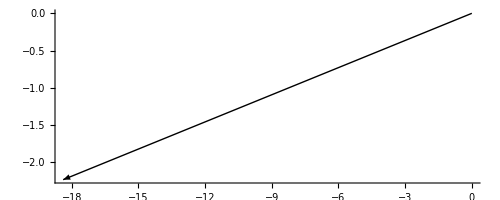

```mathematica
a[3]
```

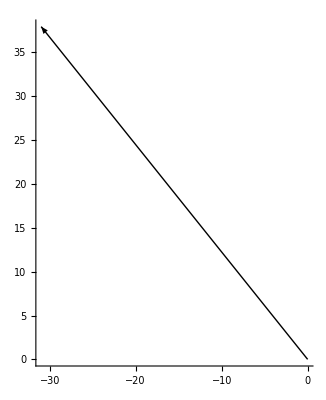

```mathematica
a[4]
```

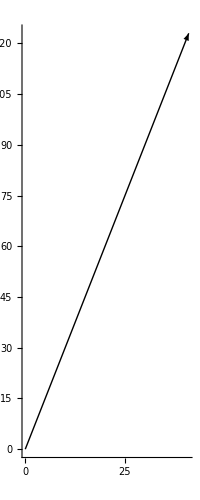

```mathematica
a[5]
```

### Exercici 4

(a) Vegem com resoldre i visualitzar el càlcul de les arrels d' un nombre complex w. Per exemple

```mathematica
n = 3
w=1
solns = Solve[z^n == w,z]
rules = N[solns]
```

3

1

{{z→1},{z→-(-1)^(1/3)},{z→(-1)^(2/3)}}

{{z→1.},{z→-0.5-0.866025 ⅈ},{z→-0.5+0.866025 ⅈ}}

Dibuixem les solucions i les connectem amb segments

{{1.,0},{-0.5,-0.866025},{-0.5,0.866025}}

{{1.,0},{-0.5,-0.866025},{-0.5,0.866025},{1.,0}}

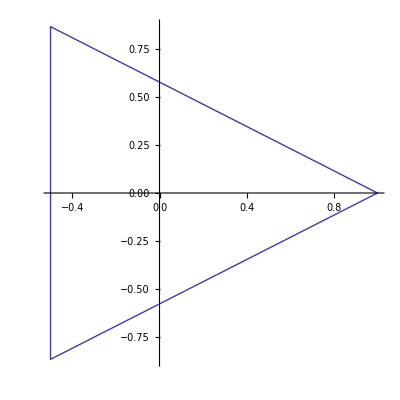

```mathematica
roots = Table[{Re[z /. rules[[ii]]], Im[z /. rules[[ii]]]},
  {ii, 1, n}]
roots = Append[roots, First[roots]]
ListPlot[roots, PlotJoined -> True, AspectRatio -> 1]
```

(b) Calculeu i dibuixeu les arrels n-èsimes de w, amb

```mathematica
n=4
w=1
```

4

1

```mathematica
solns = Solve[z^n == w,z]
rules = N[solns]
```

{{z→-1},{z→-ⅈ},{z→ⅈ},{z→1}}

{{z→-1.},{z→0.-1. ⅈ},{z→0.+1. ⅈ},{z→1.}}

{{-1.,0},{0.,-1.},{0.,1.},{1.,0}}

{{-1.,0},{0.,-1.},{0.,1.},{1.,0},{-1.,0}}

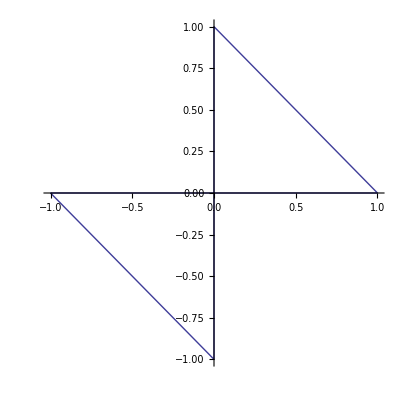

```mathematica
roots = Table[{Re[z /. rules[[ii]]], Im[z /. rules[[ii]]]},
  {ii, 1, n}]
roots = Append[roots, First[roots]]
ListPlot[roots, PlotJoined -> True, AspectRatio -> 1]
```

```mathematica
n=7
w=8
```

7

8

```mathematica
solns = Solve[z^n == w,z]
rules = N[solns]
```

{{z→-(-2)^(3/7)},{z→2^(3/7)},{z→-(-1)^(1/7) 2^(3/7)},{z→(-1)^(2/7) 2^(3/7)},{z→(-1)^(4/7) 2^(3/7)},{z→-(-1)^(5/7) 2^(3/7)},{z→(-1)^(6/7) 2^(3/7)}}

{{z→-0.299491-1.31216 ⅈ},{z→1.3459},{z→-1.21261-0.583964 ⅈ},{z→0.839155+1.05227 ⅈ},{z→-0.299491+1.31216 ⅈ},{z→0.839155-1.05227 ⅈ},{z→-1.21261+0.583964 ⅈ}}

{{-0.299491,-1.31216},{1.3459,0},{-1.21261,-0.583964},{0.839155,1.05227},{-0.299491,1.31216},{0.839155,-1.05227},{-1.21261,0.583964}}

{{-0.299491,-1.31216},{1.3459,0},{-1.21261,-0.583964},{0.839155,1.05227},{-0.299491,1.31216},{0.839155,-1.05227},{-1.21261,0.583964},{-0.299491,-1.31216}}

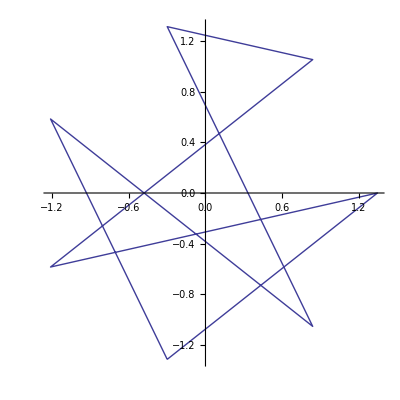

```mathematica
roots = Table[{Re[z /. rules[[ii]]], Im[z /. rules[[ii]]]},
  {ii, 1, n}]
roots = Append[roots, First[roots]]
ListPlot[roots, PlotJoined -> True, AspectRatio -> 1]
```

```mathematica
n=23
w=2
```

23

2

```mathematica
solns = Solve[z^n == w,z]
rules = N[solns]
```

{{z→-(-2)^(1/23)},{z→2^(1/23)},{z→(-1)^(2/23) 2^(1/23)},{z→-(-1)^(3/23) 2^(1/23)},{z→(-1)^(4/23) 2^(1/23)},{z→-(-1)^(5/23) 2^(1/23)},{z→(-1)^(6/23) 2^(1/23)},{z→-(-1)^(7/23) 2^(1/23)},{z→(-1)^(8/23) 2^(1/23)},{z→-(-1)^(9/23) 2^(1/23)},{z→(-1)^(10/23) 2^(1/23)},{z→-(-1)^(11/23) 2^(1/23)},{z→(-1)^(12/23) 2^(1/23)},{z→-(-1)^(13/23) 2^(1/23)},{z→(-1)^(14/23) 2^(1/23)},{z→-(-1)^(15/23) 2^(1/23)},{z→(-1)^(16/23) 2^(1/23)},{z→-(-1)^(17/23) 2^(1/23)},{z→(-1)^(18/23) 2^(1/23)},{z→-(-1)^(19/23) 2^(1/23)},{z→(-1)^(20/23) 2^(1/23)},{z→-(-1)^(21/23) 2^(1/23)},{z→(-1)^(22/23) 2^(1/23)}}

{{z→-1.021-0.140333 ⅈ},{z→1.0306},{z→0.992378+0.278051 ⅈ},{z→-0.945274-0.41059 ⅈ},{z→0.880561+0.535481 ⅈ},{z→-0.799445-0.650396 ⅈ},{z→0.703436+0.753196 ⅈ},{z→-0.594324-0.841966 ⅈ},{z→0.474141+0.915051 ⅈ},{z→-0.345125-0.97109 ⅈ},{z→0.209681+1.00904 ⅈ},{z→-0.0703303-1.02819 ⅈ},{z→-0.0703303+1.02819 ⅈ},{z→0.209681-1.00904 ⅈ},{z→-0.345125+0.97109 ⅈ},{z→0.474141-0.915051 ⅈ},{z→-0.594324+0.841966 ⅈ},{z→0.703436-0.753196 ⅈ},{z→-0.799445+0.650396 ⅈ},{z→0.880561-0.535481 ⅈ},{z→-0.945274+0.41059 ⅈ},{z→0.992378-0.278051 ⅈ},{z→-1.021+0.140333 ⅈ}}

{{-1.021,-0.140333},{1.0306,0},{0.992378,0.278051},{-0.945274,-0.41059},{0.880561,0.535481},{-0.799445,-0.650396},{0.703436,0.753196},{-0.594324,-0.841966},{0.474141,0.915051},{-0.345125,-0.97109},{0.209681,1.00904},{-0.0703303,-1.02819},{-0.0703303,1.02819},{0.209681,-1.00904},{-0.345125,0.97109},{0.474141,-0.915051},{-0.594324,0.841966},{0.703436,-0.753196},{-0.799445,0.650396},{0.880561,-0.535481},{-0.945274,0.41059},{0.992378,-0.278051},{-1.021,0.140333}}

{{-1.021,-0.140333},{1.0306,0},{0.992378,0.278051},{-0.945274,-0.41059},{0.880561,0.535481},{-0.799445,-0.650396},{0.703436,0.753196},{-0.594324,-0.841966},{0.474141,0.915051},{-0.345125,-0.97109},{0.209681,1.00904},{-0.0703303,-1.02819},{-0.0703303,1.02819},{0.209681,-1.00904},{-0.345125,0.97109},{0.474141,-0.915051},{-0.594324,0.841966},{0.703436,-0.753196},{-0.799445,0.650396},{0.880561,-0.535481},{-0.945274,0.41059},{0.992378,-0.278051},{-1.021,0.140333},{-1.021,-0.140333}}

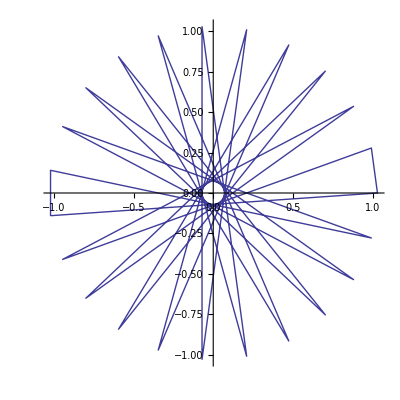

```mathematica
roots = Table[{Re[z /. rules[[ii]]], Im[z /. rules[[ii]]]},
  {ii, 1, n}]
roots = Append[roots, First[roots]]
ListPlot[roots, PlotJoined -> True, AspectRatio -> 1]
```

```mathematica
n=4
w=-1
```

4

-1

```mathematica
solns = Solve[z^n == w,z]
rules = N[solns]
```

{{z→-(-1)^(1/4)},{z→(-1)^(1/4)},{z→-(-1)^(3/4)},{z→(-1)^(3/4)}}

{{z→-0.707107-0.707107 ⅈ},{z→0.707107+0.707107 ⅈ},{z→0.707107-0.707107 ⅈ},{z→-0.707107+0.707107 ⅈ}}

{{-0.707107,-0.707107},{0.707107,0.707107},{0.707107,-0.707107},{-0.707107,0.707107}}

{{-0.707107,-0.707107},{0.707107,0.707107},{0.707107,-0.707107},{-0.707107,0.707107},{-0.707107,-0.707107}}

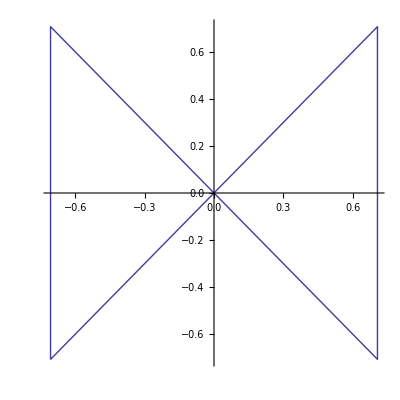

```mathematica
roots = Table[{Re[z /. rules[[ii]]], Im[z /. rules[[ii]]]},
  {ii, 1, n}]
roots = Append[roots, First[roots]]
ListPlot[roots, PlotJoined -> True, AspectRatio -> 1]
```

(c) Intenteu modificar les línies anteriors per tal que Mathematica retorni com resultat el dibuix d'un polígon regular

{{√(5/8+(√5)/8),1/4 (-1+√5)},{√(5/8-(√5)/8),1/4 (-1-√5)},{-√(5/8-(√5)/8),1/4 (-1-√5)},{-√(5/8+(√5)/8),1/4 (-1+√5)},{0,1}}

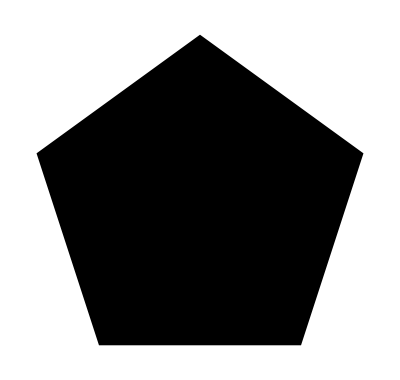

```mathematica
pentagon=Table[{Sin[2 Pi n/5],Cos[2 Pi n/5]},{n,5}]
Graphics[Polygon[pentagon]]
```